Your Title Here

```mathematica
P=1;(*bar*)
Psat1[temp_]:=10^(5.31301-1676.569/(temp+251.272));(*methanol*)
Psat2[temp_]:=10^(4.6542-1435.264/(temp+208.152));(*water*)
```

```mathematica
A12=0.7923;A21=0.5434;
γ1[x_]:=Exp[(1-x)^2*(A12+2*(A21-A12)*x)];
γ2[x_]:=Exp[x^2*(A21+2*(A12-A21)*(1-x))];
```

```mathematica
equilb=Quiet@Interpolation[{#,y/.Quiet@FindRoot[{y==(#*γ1[#]*Psat1[temp])/P,P==#*γ1[#]*Psat1[temp]+(1-#)*γ2[#]*Psat2[temp]},{{y,0},{temp,100}}]}&/@Range[0,1,0.05]];
```

```mathematica
xybase=Plot[{equilb[x],x},{x,0,1},PlotStyle->{{Thick,Black}},PlotRange->{{0,1},{0,1}},
Frame->True,FrameLabel->{Row@{"liquid mole fraction ",Style["x",Italic]},Row@{"vapor mole fraction ",Style["y",Italic]}},
LabelStyle->{17,Black},AspectRatio->Full,PlotRangeClipping->False];
```

```mathematica
Manipulate[
Module[{zf,xd,xb,R,feed,rect,xi,yi,Vb,strip,i,yR,xR,x1,y1,nR,yS,xS,nS,nT,coly,colx,Ry,Rx,Sy,Sx,Sr,lines,xlab,ylab,stages},
zf=0.5;xd=0.85;xb=0.05;R=1.5;
feed[x_]:=q/(q-1)*x-zf/(q-1);
rect[x_]:=R/(R+1)*x+xd/(R+1);
xi=x/.Quiet@FindRoot[feed[x]==rect[x],{x,0.7}];yi=rect[xi];

Vb=(xb-xi)/(xi-yi);
strip[x_]:=(Vb+1)/Vb*x-1/Vb*xb;(*strip[x_]:=yi+(x-xi)/(xb-xi)*(xb-yi);*)

(*RECTIFYING*)
i=0;yR[0]=xd;xR[0]=xd;
While[xR[i]>xi,{x1=x/.Quiet@FindRoot[yR[i]==equilb[x],{x,0.7}],y1=rect[x1],If[x1>xi,{xR[i+1]=x1,yR[i+1]=y1}],i++}];
nR=i-1;

(*STRIPPING*)
i=0;yS[0]=yR[nR];xS[0]=xR[nR];
While[xS[i]>xb,{x1=x/.Quiet@FindRoot[yS[i]==equilb[x],{x,0.5}],y1=strip[x1],xS[i+1]=x1,yS[i+1]=y1,i++}];
nS=i-1;
nT=nR+nS+1;

coly=Purple;colx=RGBColor[0,0.6,0];
(*R STAGES*)
Ry={coly,Line[{{xR[#],yR[#-1]},{xR[#],yR[#]}}]}&/@Range@nR;
Rx={colx,Line[{{xR[#],yR[#]},{xR[#+1],yR[#]}}]}&/@If[nR≥1,Range[0,nR-1],{0}];
(*S STAGES*)
Sy={coly,Line[{{xS[#+1],yS[#]},{xS[#+1],yS[#+1]}}]}&/@Range[0,nS-1];
Sx={colx,Line[{{xS[#-1],yS[#-1]},{xS[#],yS[#-1]}}]}&/@Range[nS+1];
Sr={coly,Line[{{xS[nS+1],yS[nS]},{xS[nS+1],xS[nS+1]}}]};

lines=Show[
Plot[feed[x],{x,xi,zf},PlotStyle->{Thick,Blue}],
Plot[rect[x],{x,xi,xd},PlotStyle->{Thick,RGBColor[1,0.4,0]}],
Plot[strip[x],{x,xb,xi},PlotStyle->{Thick,Hue@0.9}]
];

xlab=Riffle[ReplacePart[Join[{{1,"D",1}},Round[{#,0.5*(#-1),0.5*(#+1)}]&/@Range[3,2*nT-1,2]],nT->{2*nT-1,nT-1,"B"}],ConstantArray[{0,0,0},nT]];
ylab=Riffle[ConstantArray[{0,0},nT],Round[{#,0.5*#}]&/@Range[2,2*nT,2]];

stages=Graphics[{
{Thick,Take[Join[Riffle[Rx,Ry],Riffle[Sx,Sy],{Sr},ConstantArray[{},5]],step]},
Insert[DeleteDuplicates@Take[Riffle[#,#]&@Join[
Text[Style[Subscript[Style["y",Italic],#],18],{xR[#],yR[#-1]},{1,-1}]&/@Range@nR,
Text[Style[Subscript[Style["y",Italic],nR+#],18],{xS[#],yS[#-1]},{1,-1}]&/@Range@nS,
{Text[Style[Subscript[Style["y",Italic],"B"],18,Background->White],{xS[nS+1],yS[nS]},{0,-1}]},ConstantArray[{},5]],
step],Which[step≥2*nT,Black,OddQ@step,colx,EvenQ@step,coly],If[step<2*nT,{1,1,1,2,2,3,3,4,4,5,5}[[step+1]],1]],
Insert[DeleteDuplicates@Take[Join[
{Text[Style[Subscript[Style["x",Italic],"D"],18,Background->White],{xR[0],yR[0]},1.5*{-1,0}]},
Riffle[#,#]&@Join[
Text[Style[Subscript[Style["x",Italic],#],18,Background->White],{xR[#],yR[#]},1.5*{-1,0}]&/@Range@nR,
Text[Style[Subscript[Style["x",Italic],nR+#],18,Background->White],{xS[#],yS[#]},1.5*{-1,0}]&/@Range@nS],ConstantArray[{},5]],
step],Which[step≥2*nT,Black,OddQ@step,colx,EvenQ@step,coly],If[step<2*nT,{1,1,2,2,3,3,4,4,5,5}[[step+1]],1]],
If[0<step<2*nT,Text[If[OddQ@step,
Style[Column[{"material balance between stages",
Row@{"relates ",Subscript[Style["x",Italic],xlab[[step,2]]]," to ",Subscript[Style["y",Italic],xlab[[step,3]]]}
},Center],17,colx],
Style[Column[{"on the stage",
Row@{"liquid ",Subscript[Style["x",Italic],ylab[[step,2]]]," is in VLE with vapor ",Subscript[Style["y",Italic],ylab[[step,2]]]}
},Center],17,coly]
],{0.55,0.07}]]
}];

Show[xybase,lines,stages,ImageSize->{350,435}]
],
Control[{{q,0.5,"feed quality"},-0.2,1.5,0.1,Appearance->"Labeled",Exclusions->1}],
Control[{{step,0,"step off stages"},0,10,1,Appearance->"Labeled"}],
SaveDefinitions->True]
```

```mathematica
(*colx*)
```

```mathematica
{{1,"D",1},{3,1,2},{5,2,3},{2*nT-1,3,"B"}}
```

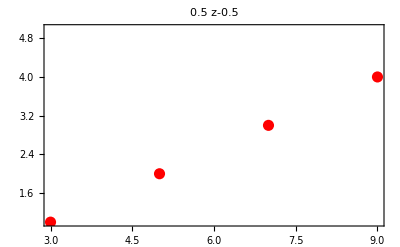
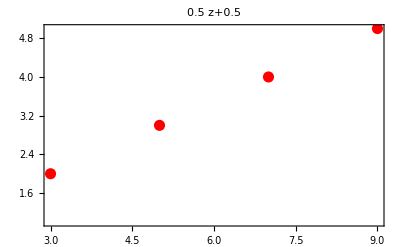

```mathematica
Module[{L1,L2,L3,f2,f3,opt},
L1={{3,1,2},{5,2,3},{7,3,4},{9,4,5}};
L2={L1[[#,1]],L1[[#,2]]}&/@Range@Length@L1;
L3={L1[[#,1]],L1[[#,3]]}&/@Range@Length@L1;

f2=Fit[L2,{1,t},t]/.t->z;
f3=Fit[L3,{1,t},t]/.t->z;

opt=Sequence[PlotStyle->{Thick,Black},PlotRange->{{3,9},{1,5}},PlotRangePadding->Scaled@0.02,Frame->True,LabelStyle->{17,Black},ImageSize->400];

{Plot[f2[z],{z,3,9},Evaluate@opt,PlotLabel->f2,Epilog->{Red,PointSize@0.02,Point@L2}],
Plot[f3[z],{z,3,9},Evaluate@opt,PlotLabel->f3,Epilog->{Red,PointSize@0.02,Point@L3}]}
]
```

```mathematica
x={{3,1,2},{5,2,3},{7,3,4},{9,4,5}}
```

```mathematica
x1={{3,1},{5,2},{7,3},{9,4}}
```

```mathematica
x2={{3,2},{5,3},{7,4},{9,5}}
```

```mathematica
Manipulate[
Module[{x},
x=ReplacePart[Join[{{1,"D",1}},{#,0.5*(#-1),0.5*(#+1)}&/@Range[3,2*nT-1,2]],nT->{2*nT-1,nT-1,"B"}];
Column[{x,Spacer@0,
Riffle[ReplacePart[Join[{{1,"D",1}},Round[{#,0.5*(#-1),0.5*(#+1)}]&/@Range[3,2*nT-1,2]],nT->{2*nT-1,nT-1,"B"}],ConstantArray[{0,0,0},nT]]
}]
],
Control[{{nT,4,"total stages"},3,5,1,Appearance->"Labeled"}],
Control[{{step,0,"step off stages"},0,10,1,Appearance->"Labeled"}]
]
```

```mathematica
(*coly*)
```

```mathematica
{{2,1,1},{4,2,2},{6,3,3},{8,4,4}}
```

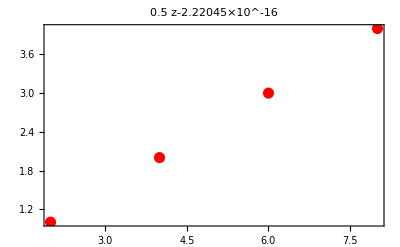
{-Graphics-,-Graphics-}

```mathematica
Module[{L1,L2,L3,f2,f3,opt},
L1={{2,1,1},{4,2,2},{6,3,3},{8,4,4}};
L2={L1[[#,1]],L1[[#,2]]}&/@Range@Length@L1;
L3={L1[[#,1]],L1[[#,3]]}&/@Range@Length@L1;

f2=Fit[L2,{1,t},t]/.t->z;
f3=Fit[L3,{1,t},t]/.t->z;

opt=Sequence[PlotStyle->{Thick,Black},PlotRange->{{2,8},{1,4}},PlotRangePadding->Scaled@0.02,Frame->True,LabelStyle->{17,Black},ImageSize->400];

{Plot[f2[z],{z,2,8},Evaluate@opt,PlotLabel->f2,Epilog->{Red,PointSize@0.02,Point@L2}],
Plot[f3[z],{z,2,8},Evaluate@opt,PlotLabel->f3,Epilog->{Red,PointSize@0.02,Point@L3}]}
]
```

```mathematica
y={{2,1,1},{4,2,2},{6,3,3},{8,4,4}};
```

```mathematica
y1={{2,1},{4,2},{6,3},{8,4}};
```

```mathematica
y2={{2,1},{4,2},{6,3},{8,4}};
```





```mathematica
Manipulate[
Module[{y},
y=Riffle[ConstantArray[{0,0,0},nT],Round[{#,0.5*#,0.5*#}]&/@Range[2,2*nT,2]];
Riffle[ConstantArray[{0,0},nT],Round[{#,0.5*#}]&/@Range[2,2*nT,2]]
],
Control[{{nT,4,"total stages"},3,5,1,Appearance->"Labeled"}],
Control[{{step,0,"step off stages"},0,10,1,Appearance->"Labeled"}]
]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX